5

pdf

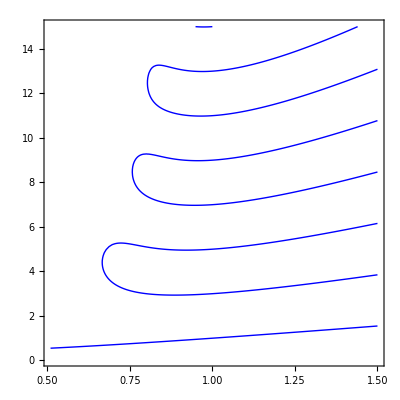

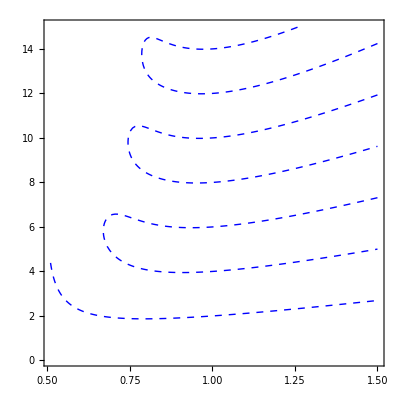

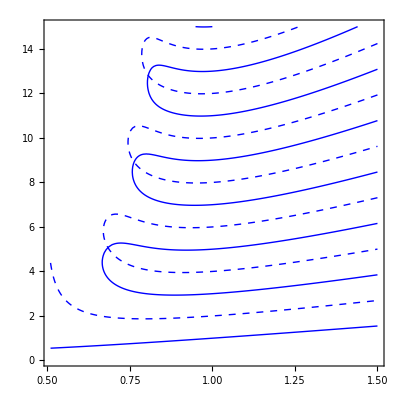

HOZeroesRie.pdf

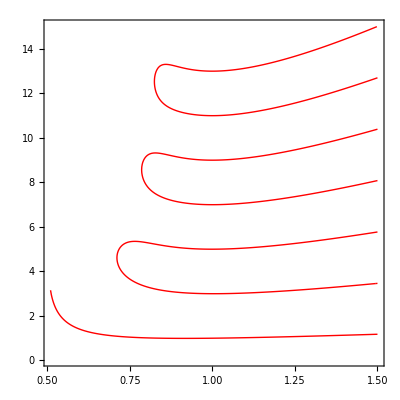

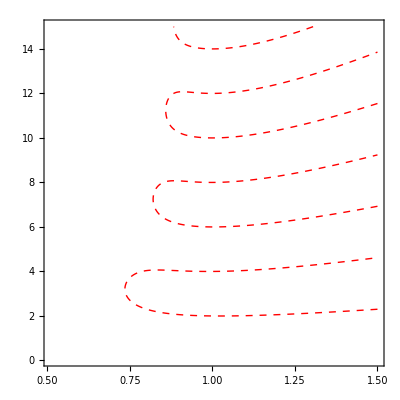

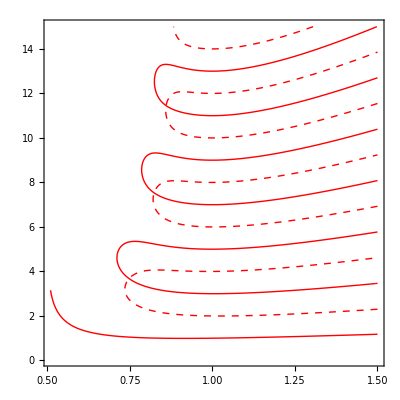

HOZeroesCap.pdf

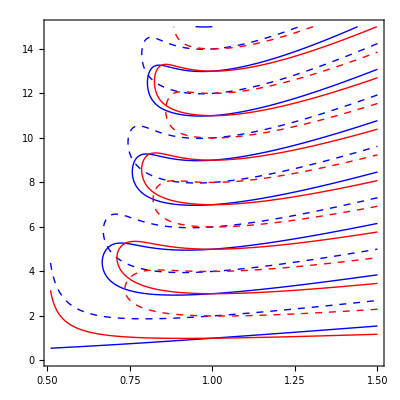

ⅇ^((ⅈ π)/(2 alp))

ⅇ^(-(ⅈ π)/(2 alp))

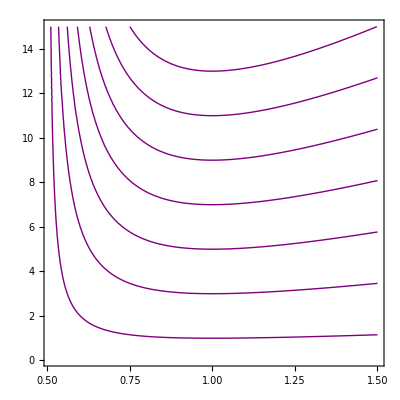

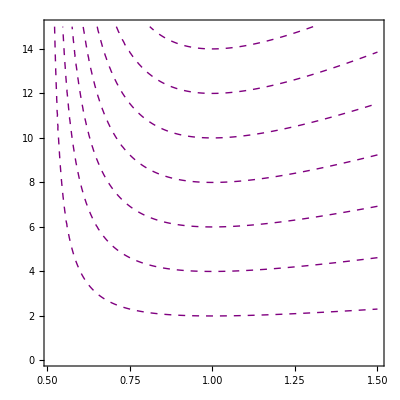

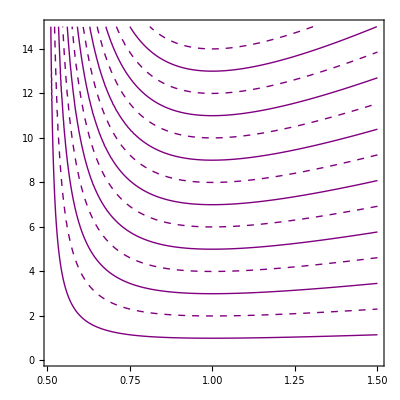

HOZeroesFou.pdf

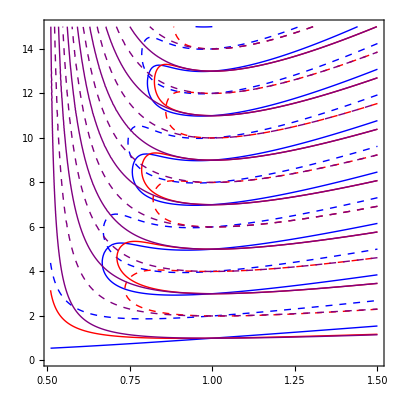

totalRCF

totalRCF.pdf

0.75

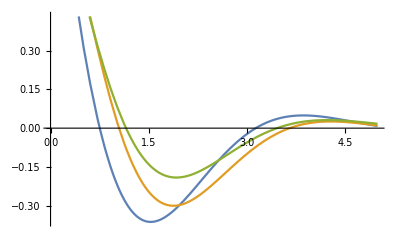

```mathematica
Clear[alp]
prec = 5
exportDataType="pdf"
(* Riemann  *)
name = "HOZeroesRie";
sinR[x_] = x^(2 alp -1)MittagLefflerE[2 alp, 2 alp, -x^(2 alp)];
cosR[x_] = x^(alp-1)MittagLefflerE[2 alp,  alp, -x^(2 alp)];
pcR = ContourPlot[cosR[x Pi/2]==0,{alp,0.51,1.5},{x,0.05,15},ContourStyle->{Blue,Thick},MaxRecursion->prec]
psR = ContourPlot[sinR[x Pi/2]==0,{alp,0.51,1.5},{x,0.05,15},ContourStyle->{Blue,Dashed,Thick},MaxRecursion->prec]
(*final output*)
fin = Show[{pcR,psR}]
Export[name<>"."<>exportDataType,fin]

(* Caputo  *)
name = "HOZeroesCap";
sinC[x_] = x^(a)MittagLefflerE[2 alp, 1+ alp, -x^(2 alp)];
cosC[x_] = MittagLefflerE[2 alp, -x^(2 alp)];
pcC = ContourPlot[cosC[x Pi/2]==0,{alp,0.51,1.5},{x,0.05,15},ContourStyle->{Red,Thick},MaxRecursion->prec]
psC = ContourPlot[sinC[x Pi/2]==0,{alp,0.51,1.5},{x,0.05,15},ContourStyle->{Red,Dashed,Thick},MaxRecursion->prec]
(*final output*)
fin = Show[{pcC,psC}]
Export[name<>"."<>exportDataType,fin]

totalRC = Show[{pcR,psR,pcC,psC}]

(* Fourier  *)
name = "HOZeroesFou";
fp =  Exp[+I Pi/( 2alp)]
fm =  Exp[-I Pi/( 2alp)]
sinF[x_] = 1/(2 I)(Exp[fp x]- Exp[fm x]);
cosF[x_] = 1/2(Exp[fp x]+ Exp[fm x]);
pcF = ContourPlot[cosF[x Pi/2]==0,{alp,0.51,1.5},{x,0.05,15},ContourStyle->{Purple,Thick},MaxRecursion->prec]
psF = ContourPlot[sinF[x Pi/2]==0,{alp,0.51,1.5},{x,0.05,15},ContourStyle->{Purple,Dashed,Thick},MaxRecursion->prec]
(*final output*)
fin = Show[{pcF,psF}]
Export[name<>"."<>exportDataType,fin]
totalRCF = Show[{pcR,psR,pcC,psC,pcF,psF}]

name = "totalRCF"
Export[name<>"."<>exportDataType,fin]
alp = 0.75
Plot[{cosR[x Pi/2], cosC[x Pi/2],cosF[x Pi/2]},{x,0,5}]
```